```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_],LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"C:\\Users\\vfigu\\OneDrive\\Documentos\\vvfigueira.github.io\\WolframWindows\\Teste1\\ScalarProxy"]
```

Successfully patched FeynArts.

```mathematica
diags=InsertFields[CreateTopologies[0,2->3],{S[1],S[1]}->{S[1],S[1],S[1]},InsertionLevel->{Classes},Model->"C:\\Users\\vfigu\\OneDrive\\Documentos\\vvfigueira.github.io\\WolframWindows\\Teste1\\ScalarProxy\\ScalarProxy", GenericModel ->"C:\\Users\\vfigu\\OneDrive\\Documentos\\vvfigueira.github.io\\WolframWindows\\Teste1\\ScalarProxy\\ScalarProxy"];
```

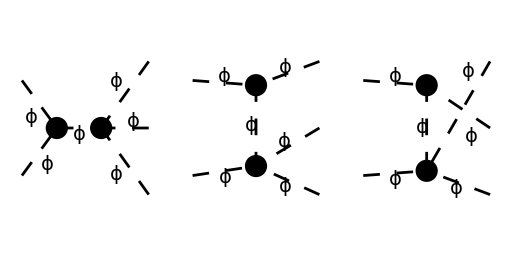

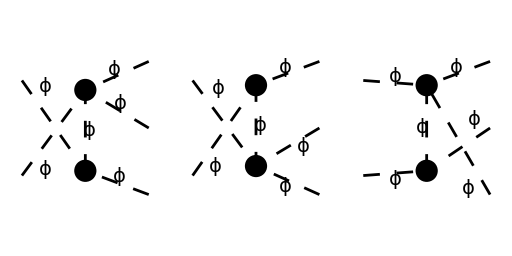

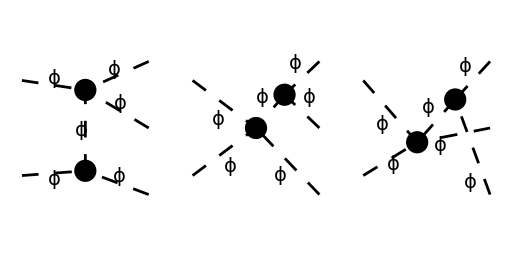

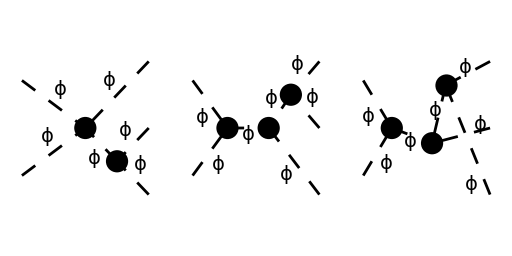

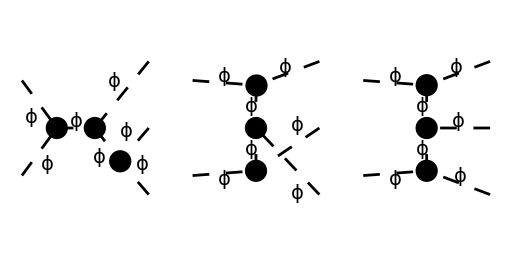

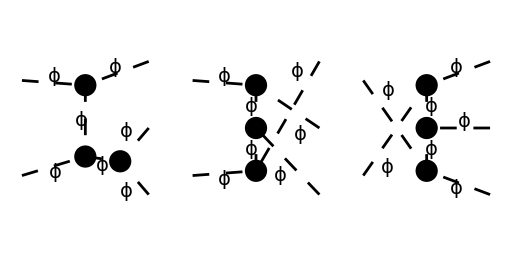

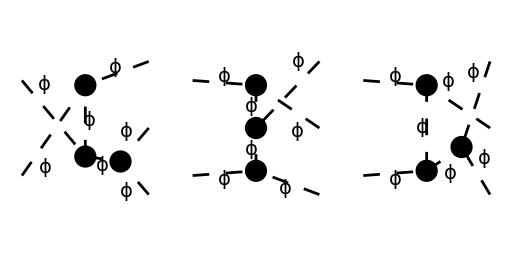

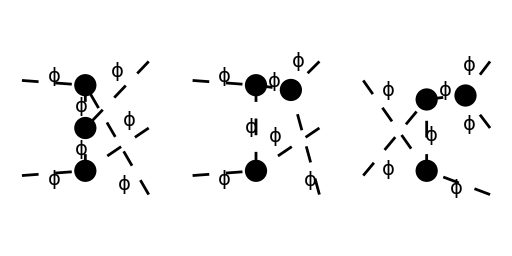

```mathematica
Paint[diags,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{-p1,-p2},OutgoingMomenta->{l1,l2,l3},LoopMomenta->{},ChangeDimension->4,List->False];
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[x,{ p1 , p2, l1 , l2 ,l3} ,{0 , 0 , m , m,m} ];
```

```mathematica
amp[1]=amp[0] // Contract // SUNSimplify;
```

```mathematica
amp[2] = amp[1] // ExpandScalarProduct;
```

```mathematica
amp[3] =FeynAmpDenominatorExplicit[amp[2]]
```

-(3 g^2 (ⅈ g m^2-ⅈ g x[1,2]))/(x[1,2] (-m^2+x[1,2]))+(3 ⅈ g^3)/(-m^2+x[1,5])+(3 ⅈ g^3)/(-m^2+x[2,3])+(g^2 (-ⅈ g x[1,5]-ⅈ g x[2,3]))/((-m^2+x[1,5]) (-m^2+x[2,3]))+(3 ⅈ g^3)/(m^2+x[1,5]-x[2,3]-x[3,4])+(g^2 (-ⅈ g x[1,5]-ⅈ g (2 m^2+x[1,5]-x[2,3]-x[3,4])))/((-m^2+x[1,5]) (m^2+x[1,5]-x[2,3]-x[3,4]))+(3 ⅈ g^3)/(-x[1,2]-x[1,5]+x[3,4])-(3 g^2 (-ⅈ g m^2-ⅈ g x[3,4]))/(x[3,4] (-m^2+x[3,4]))-((ⅈ g m^2-ⅈ g x[1,2]) (-ⅈ g m^2-ⅈ g x[3,4]) (-ⅈ g x[1,2]-ⅈ g x[3,4]))/(x[1,2] (-m^2+x[1,2]) x[3,4] (-m^2+x[3,4]))+(ⅈ g (-ⅈ g m^2-ⅈ g x[3,4]) (ⅈ g m^2-ⅈ g x[1,5]-ⅈ g x[3,4]))/((-m^2+x[1,5]) x[3,4] (-m^2+x[3,4]))+(ⅈ g (-ⅈ g m^2-ⅈ g x[3,4]) (ⅈ g m^2-ⅈ g x[3,4]-ⅈ g (m^2-x[1,2]-x[1,5]+x[3,4])))/(x[3,4] (-m^2+x[3,4]) (-x[1,2]-x[1,5]+x[3,4]))+(3 ⅈ g^3)/(m^2-x[1,5]+x[2,3]-x[4,5])+(g^2 (-ⅈ g x[2,3]-ⅈ g (2 m^2-x[1,5]+x[2,3]-x[4,5])))/((-m^2+x[2,3]) (m^2-x[1,5]+x[2,3]-x[4,5]))+(g^2 (-ⅈ g (m^2-x[1,2]-x[1,5]+x[3,4])-ⅈ g (2 m^2-x[1,5]+x[2,3]-x[4,5])))/((-x[1,2]-x[1,5]+x[3,4]) (m^2-x[1,5]+x[2,3]-x[4,5]))-(3 g^2 (-ⅈ g m^2-ⅈ g (3 m^2+x[1,2]-x[3,4]-x[4,5])))/((2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))-((ⅈ g m^2-ⅈ g x[1,2]) (-ⅈ g m^2-ⅈ g (3 m^2+x[1,2]-x[3,4]-x[4,5])) (-ⅈ g x[1,2]-ⅈ g (3 m^2+x[1,2]-x[3,4]-x[4,5])))/(x[1,2] (-m^2+x[1,2]) (2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))+(ⅈ g (-ⅈ g m^2-ⅈ g (3 m^2+x[1,2]-x[3,4]-x[4,5])) (ⅈ g m^2-ⅈ g (2 m^2+x[1,5]-x[2,3]-x[3,4])-ⅈ g (3 m^2+x[1,2]-x[3,4]-x[4,5])))/((m^2+x[1,5]-x[2,3]-x[3,4]) (2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))+(ⅈ g (-ⅈ g m^2-ⅈ g (3 m^2+x[1,2]-x[3,4]-x[4,5])) (ⅈ g m^2-ⅈ g (2 m^2-x[1,5]+x[2,3]-x[4,5])-ⅈ g (3 m^2+x[1,2]-x[3,4]-x[4,5])))/((m^2-x[1,5]+x[2,3]-x[4,5]) (2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))+(3 ⅈ g^3)/(-x[1,2]-x[2,3]+x[4,5])-(3 g^2 (-ⅈ g m^2-ⅈ g x[4,5]))/(x[4,5] (-m^2+x[4,5]))-((ⅈ g m^2-ⅈ g x[1,2]) (-ⅈ g m^2-ⅈ g x[4,5]) (-ⅈ g x[1,2]-ⅈ g x[4,5]))/(x[1,2] (-m^2+x[1,2]) x[4,5] (-m^2+x[4,5]))+(ⅈ g (-ⅈ g m^2-ⅈ g x[4,5]) (ⅈ g m^2-ⅈ g x[2,3]-ⅈ g x[4,5]))/((-m^2+x[2,3]) x[4,5] (-m^2+x[4,5]))+(g^2 (-ⅈ g (2 m^2+x[1,5]-x[2,3]-x[3,4])-ⅈ g (m^2-x[1,2]-x[2,3]+x[4,5])))/((m^2+x[1,5]-x[2,3]-x[3,4]) (-x[1,2]-x[2,3]+x[4,5]))+(g^2 (-ⅈ g (m^2-x[1,2]-x[1,5]+x[3,4])-ⅈ g (m^2-x[1,2]-x[2,3]+x[4,5])))/((-x[1,2]-x[1,5]+x[3,4]) (-x[1,2]-x[2,3]+x[4,5]))+(ⅈ g (-ⅈ g m^2-ⅈ g x[4,5]) (ⅈ g m^2-ⅈ g x[4,5]-ⅈ g (m^2-x[1,2]-x[2,3]+x[4,5])))/(x[4,5] (-m^2+x[4,5]) (-x[1,2]-x[2,3]+x[4,5]))

```mathematica
amp[4] = amp[3]// ExpandScalarProduct  // Simplify
```

ⅈ g^3 (3/x[1,2]+3/(-m^2+x[1,5])+3/(-m^2+x[2,3])-(x[1,5]+x[2,3])/((m^2-x[1,5]) (m^2-x[2,3]))-3/(x[1,2]+x[1,5]-x[3,4])+3/(m^2+x[1,5]-x[2,3]-x[3,4])+((m^2-x[1,5]-x[3,4]) (m^2+x[3,4]))/((m^2-x[1,5]) (m^2-x[3,4]) x[3,4])+(3 (m^2+x[3,4]))/(x[3,4] (-m^2+x[3,4]))+((m^2+x[3,4]) (x[1,2]+x[3,4]))/(x[1,2] (m^2-x[3,4]) x[3,4])-(-2 m^2-2 x[1,5]+x[2,3]+x[3,4])/((m^2-x[1,5]) (m^2+x[1,5]-x[2,3]-x[3,4]))-((m^2+x[3,4]) (-x[1,2]-x[1,5]+2 x[3,4]))/(x[3,4] (-m^2+x[3,4]) (-x[1,2]-x[1,5]+x[3,4]))-3/(x[1,2]+x[2,3]-x[4,5])+3/(m^2-x[1,5]+x[2,3]-x[4,5])+(3 (4 m^2+x[1,2]-x[3,4]-x[4,5]))/((2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))-((4 m^2+x[1,2]-x[1,5]+x[2,3]-x[3,4]-2 x[4,5]) (4 m^2+x[1,2]-x[3,4]-x[4,5]))/((m^2-x[1,5]+x[2,3]-x[4,5]) (2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))-((4 m^2+x[1,2]+x[1,5]-x[2,3]-2 x[3,4]-x[4,5]) (4 m^2+x[1,2]-x[3,4]-x[4,5]))/((m^2+x[1,5]-x[2,3]-x[3,4]) (2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))-((4 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+2 x[1,2]-x[3,4]-x[4,5]))/(x[1,2] (2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))+(-2 m^2+2 x[1,2]+x[1,5]+x[2,3]-x[3,4]-x[4,5])/((x[1,2]+x[1,5]-x[3,4]) (x[1,2]+x[2,3]-x[4,5]))+((m^2-x[2,3]-x[4,5]) (m^2+x[4,5]))/((m^2-x[2,3]) (m^2-x[4,5]) x[4,5])+(3 (m^2+x[4,5]))/(x[4,5] (-m^2+x[4,5]))+((m^2+x[4,5]) (x[1,2]+x[4,5]))/(x[1,2] (m^2-x[4,5]) x[4,5])-(-2 m^2+x[1,5]-2 x[2,3]+x[4,5])/((m^2-x[2,3]) (m^2-x[1,5]+x[2,3]-x[4,5]))+(3 m^2-x[1,2]+x[1,5]-2 x[2,3]-x[3,4]+x[4,5])/((m^2+x[1,5]-x[2,3]-x[3,4]) (x[1,2]+x[2,3]-x[4,5]))+(-3 m^2+x[1,2]+2 x[1,5]-x[2,3]-x[3,4]+x[4,5])/((x[1,2]+x[1,5]-x[3,4]) (-m^2+x[1,5]-x[2,3]+x[4,5]))-((m^2+x[4,5]) (-x[1,2]-x[2,3]+2 x[4,5]))/(x[4,5] (-m^2+x[4,5]) (-x[1,2]-x[2,3]+x[4,5])))

```mathematica
amp[5] = amp[4] * x[1,2]// Simplify
```

ⅈ g^3 x[1,2] (3/x[1,2]+3/(-m^2+x[1,5])+3/(-m^2+x[2,3])-(x[1,5]+x[2,3])/((m^2-x[1,5]) (m^2-x[2,3]))-3/(x[1,2]+x[1,5]-x[3,4])+3/(m^2+x[1,5]-x[2,3]-x[3,4])+((m^2-x[1,5]-x[3,4]) (m^2+x[3,4]))/((m^2-x[1,5]) (m^2-x[3,4]) x[3,4])+(3 (m^2+x[3,4]))/(x[3,4] (-m^2+x[3,4]))+((m^2+x[3,4]) (x[1,2]+x[3,4]))/(x[1,2] (m^2-x[3,4]) x[3,4])-(-2 m^2-2 x[1,5]+x[2,3]+x[3,4])/((m^2-x[1,5]) (m^2+x[1,5]-x[2,3]-x[3,4]))-((m^2+x[3,4]) (-x[1,2]-x[1,5]+2 x[3,4]))/(x[3,4] (-m^2+x[3,4]) (-x[1,2]-x[1,5]+x[3,4]))-3/(x[1,2]+x[2,3]-x[4,5])+3/(m^2-x[1,5]+x[2,3]-x[4,5])+(3 (4 m^2+x[1,2]-x[3,4]-x[4,5]))/((2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))-((4 m^2+x[1,2]-x[1,5]+x[2,3]-x[3,4]-2 x[4,5]) (4 m^2+x[1,2]-x[3,4]-x[4,5]))/((m^2-x[1,5]+x[2,3]-x[4,5]) (2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))-((4 m^2+x[1,2]+x[1,5]-x[2,3]-2 x[3,4]-x[4,5]) (4 m^2+x[1,2]-x[3,4]-x[4,5]))/((m^2+x[1,5]-x[2,3]-x[3,4]) (2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))-((4 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+2 x[1,2]-x[3,4]-x[4,5]))/(x[1,2] (2 m^2+x[1,2]-x[3,4]-x[4,5]) (3 m^2+x[1,2]-x[3,4]-x[4,5]))+(-2 m^2+2 x[1,2]+x[1,5]+x[2,3]-x[3,4]-x[4,5])/((x[1,2]+x[1,5]-x[3,4]) (x[1,2]+x[2,3]-x[4,5]))+((m^2-x[2,3]-x[4,5]) (m^2+x[4,5]))/((m^2-x[2,3]) (m^2-x[4,5]) x[4,5])+(3 (m^2+x[4,5]))/(x[4,5] (-m^2+x[4,5]))+((m^2+x[4,5]) (x[1,2]+x[4,5]))/(x[1,2] (m^2-x[4,5]) x[4,5])-(-2 m^2+x[1,5]-2 x[2,3]+x[4,5])/((m^2-x[2,3]) (m^2-x[1,5]+x[2,3]-x[4,5]))+(3 m^2-x[1,2]+x[1,5]-2 x[2,3]-x[3,4]+x[4,5])/((m^2+x[1,5]-x[2,3]-x[3,4]) (x[1,2]+x[2,3]-x[4,5]))+(-3 m^2+x[1,2]+2 x[1,5]-x[2,3]-x[3,4]+x[4,5])/((x[1,2]+x[1,5]-x[3,4]) (-m^2+x[1,5]-x[2,3]+x[4,5]))-((m^2+x[4,5]) (-x[1,2]-x[2,3]+2 x[4,5]))/(x[4,5] (-m^2+x[4,5]) (-x[1,2]-x[2,3]+x[4,5])))

```mathematica
amp[5]/.x[1,2]->0
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+3/(-m^2+x[1,5])+«22»+(3 (m^2+x[4,5]))/(x[4,5] (-m^2+x[4,5]))-(-2 m^2+x[1,5]-2 x[2,3]+x[4,5])/((m^2-x[2,3]) (m^2-x[1,5]+x[2,3]-x[4,5]))+(3 m^2+x[1,5]-2 x[2,3]-x[3,4]+x[4,5])/((m^2+x[1,5]-x[2,3]-x[3,4]) (x[2,3]-x[4,5]))+(-3 m^2+2 x[1,5]-x[2,3]-x[3,4]+x[4,5])/((x[1,5]-x[3,4]) (-m^2+x[1,5]-x[2,3]+x[4,5]))-((m^2+x[4,5]) (-x[2,3]+2 x[4,5]))/(x[4,5] (-m^2+x[4,5]) (-x[2,3]+x[4,5])) encountered.

Indeterminate

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"C:\\Users\\vfigu\\OneDrive\\Documentos\\vvfigueira.github.io\\WolframWindows\\Teste1\\ScalarProxy"]
```

Successfully patched FeynArts.

```mathematica
diags=InsertFields[CreateTopologies[1,1->1,ExcludeTopologies->Tadpoles],{S[1]}->{S[1]},InsertionLevel->{Classes},Model->"C:\\Users\\vfigu\\OneDrive\\Documentos\\vvfigueira.github.io\\WolframWindows\\Teste1\\ScalarProxy\\ScalarProxy", GenericModel ->"C:\\Users\\vfigu\\OneDrive\\Documentos\\vvfigueira.github.io\\WolframWindows\\Teste1\\ScalarProxy\\ScalarProxy"];
```

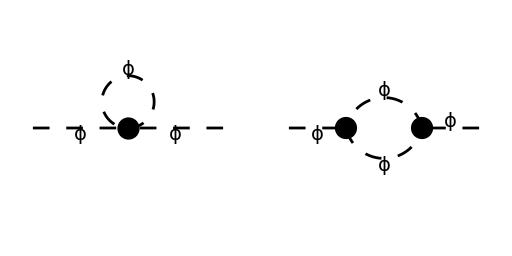

```mathematica
Paint[diags,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{p1},OutgoingMomenta->{p1},LoopMomenta->{},ChangeDimension->4,List->False];
```

```mathematica
amp[3] =FeynAmpDenominatorExplicit[amp[0]]
```

-((3 g^2)/(2 Pair[Momentum[LoopMom1],Momentum[LoopMom1]] (-m^2+Pair[Momentum[LoopMom1],Momentum[LoopMom1]])))-((ⅈ g m^2-ⅈ g Pair[Momentum[LoopMom1],Momentum[LoopMom1]]-ⅈ g Pair[Momentum[LoopMom1-p1],Momentum[LoopMom1-p1]]-ⅈ g Pair[Momentum[p1],Momentum[p1]]) (ⅈ g m^2-ⅈ g Pair[Momentum[LoopMom1],Momentum[LoopMom1]]-ⅈ g Pair[Momentum[p1],Momentum[p1]]-ⅈ g Pair[Momentum[-LoopMom1+p1],Momentum[-LoopMom1+p1]]))/(2 Pair[Momentum[LoopMom1],Momentum[LoopMom1]] (-m^2+Pair[Momentum[LoopMom1],Momentum[LoopMom1]]) (Pair[Momentum[LoopMom1],Momentum[LoopMom1]]-2 Pair[Momentum[LoopMom1],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]) (-m^2+Pair[Momentum[LoopMom1],Momentum[LoopMom1]]-2 Pair[Momentum[LoopMom1],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]))